## Типовой расчет по теории вероятностей.

### Задача 1

Одновременно подбрасывают две игральные кости. Найти вероятность того, что сумма выпавших очков 1) равна k, 2) меньше k+1, 3) больше k-1, 4)заключена в промежутке [α,β].

##### Дано :

k=5, [α,β]=[3,7]

```mathematica
Grid[Table[If [i==j==0,,i+j],{i,0,6},{j,0,6}],Frame-> All,Spacings->{1, 1}]
```

Таблица суммы выпавших очков:

| 1 | 2 | 3 | 4 | 5 | 6
1 | 2 | 3 | 4 | 5 | 6 | 7
2 | 3 | 4 | 5 | 6 | 7 | 8
3 | 4 | 5 | 6 | 7 | 8 | 9
4 | 5 | 6 | 7 | 8 | 9 | 10
5 | 6 | 7 | 8 | 9 | 10 | 11
6 | 7 | 8 | 9 | 10 | 11 | 12

1) Используя классическое определение вероятности, найдем вероятность, что сумма выпавших очков равна 5:

P(∑=5)=(N_(∑= 5))/N=4/64=0.0625

2) Вероятность, что сумма меньше 6:

P(∑<6)=(N_(∑<6))/N=10/64=0.15625

3) Вероятность, что сумма больше 4:

P(∑>4)=(N_(∑>4))/N=(64-6)/64=0.90625

4) Вероятность, что сумма в промежутке от 3 до 7:

P(3≤ ∑≤ 7)=(N_(3≤ ∑≤ 7))/N=(64-16)/64=0.75

### Задача 2

На некоторое обслуживающее устройство поступает две заявки. Каждая может поступить в любой момент времени в течение Т минут. Время обслуживания первой заявки t_1 минут, второй t_2 минут. При поступлении заявки на занятое устройство она не принимается. При поступлении ее хотя бы в последний последний момент времени Т она обслуживается. Найти вероятность того, что 1)обе заявки будут обслужены, 2) будет обслужена одна заявка.

Дано:

T=100, t_1=5, t_2=15

Пусть x- время поступления первой заявки, y- время поступления второй.

Тогда первая не будет обслужена если:

y<x<y+15

Вторая не будет обслужена:

x<y<x+5

Тогда, чтобы найти вероятность того, что будет обслужена одна заявка, надо найти площадь области удовлетворяющей условию: или не обслужена первая, или не обслужена вторая.

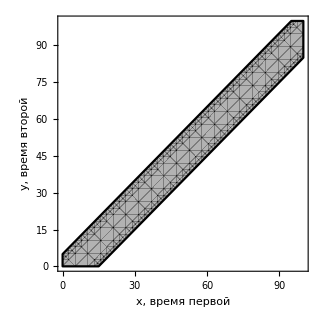

```mathematica
RegionPlot[y≤ x≤ y+15||x≤ y≤ x+5,{x,0,100},{y,0,100},Frame->True,PlotRange->{{0,100},{0,100}},FrameStyle->Thickness[0.004],PlotTheme->"Monochrome",FrameLabel->{"x, время первой","y, время второй"}]
```

Найдем эту площадь:

```mathematica
Area[ImplicitRegion[y≤x≤y+15∨x≤y≤x+5,({{x, 0, 100}, {y, 0, 100}})]]
```

1875

Тогда вероятность того, что будет обслужена одна заявка:

P(A)=1875/100^2=0.1875

Вероятность того, что будут обслужены обе:

P(Ā)=1-P(A)=0.8125

### Задача 3

Задана электрическая схема системы, состоящей из пяти элементов. Событие (Ā)_i - отказ i-ого элемента за некоторый промежуток времени. Вероятности безотказной работы элементов заданы:

P(A_i)=0.95, i=1,3,5;
P(A_i)=0.9, i=2,4.

Событие А состоит в безотказной работе всей системы за рассматриваемый промежуток времени.

Требуется: 1) Выразить событие А через А_i или (Ā)_i, 2)найти вероятность Р(А) безотказной работы системы.

1) Событие А - безотказность системы, ее можно выразить как:

A=((A_1∪A_2∪A_3)∩A_4)∪A_5

Что можно преобразовать в:

A=(A_1∩A_4)∪(A_2∩A_4)∪(A_3∩A_4)∪A_5

2) Безотказность работы блока (1 или 2 или 3) найдем по формуле:

p_123=1-∏_(i=1)^3 (1-p(A_i))=0.99975

Безотказность работы блока ((1 или 2 или 3) и 4) найдем как:

p_1234=p_123 p_4=(1-∏_(i=1)^3 (1-p(A_i)))p(A_4)=0.899775

Тогда безотказность всей системы выразим:

p(A)=1-(1-p_1234)(1-p_5)=
=1-(1-(1-∏_(i=1)^3 (1-p(A_i)))p(A_4))(1-p(A_5))=0.994989

```mathematica
p123=1-Product[1-P[i],{i,1,3}]
```

0.99975

```mathematica
p1234=p123*P[4]
```

0.899775

```mathematica
p=1-(1-p1234)(1-P[5])
```

0.994989

```mathematica
P[1]=0.95;
P[2]=0.9;
P[3]=0.95;
P[4]=0.9;
P[5]=0.95;
```

### Задача 4

Из партии содержащей n изделий, среди которых k - высшего сорта, для контроля последовательно наугад выбирают m изделий. Найти вероятность того, что среду выбранных изделий окажется ровно l высшего сорта, при условии, что выборка производится 1) с возвращением 2) без возвращения.

Дано:

n=12,k=6,m=6,l=3

1) Выборка последовательная с возвращением.

Вероятность p, того что наугад выбрано изделие высшего сорта:

p=k/n=0.5

Тогда, воспользовавшись биномиальным распределением, определим вероятность того что среди m окажется l высшего сорта:

P(A)=P_m^l=C_m^l(p^(m-l)(1-p))^l

В нашем случае:

P(A)=P_6^3=C_6^3(p^3(1-p))^3=0.3125

Эта точка будет соответствовать максимуму на графике плотности вероятности:

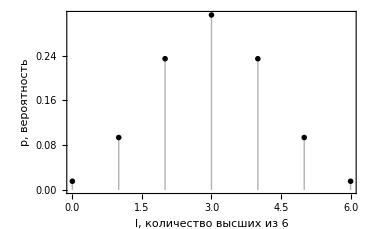

```mathematica
ListPlot[Table[{u,PDF[BinomialDistribution[6,0.5],u]},{u,0,6}],Filling->Bottom,InterpolationOrder->2,PlotTheme->"Monochrome",Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{"l, количество высших из 6", "p, вероятность"}]
```

2) Выборка последовательная без возвращения.

Всего способов выбрать m изделий:

N=С_n^m=C_12^6

Количество способов выбрать из m - l  и из (n-m)  - (m-l)  равно их произведению:

N_A=С_m^l C_(n-m)^(m-l)=C_6^3 C_6^3

Тогда используя классическое определение вероятности:

P(A)=N_A/N=(C_6^3 C_6^3)/C_12^6=100/231=0.4329

### Задача 5

На склад поступали детали, изготовляемые на трех станках. Изготовлена на станках деталей, %: 
на первом - a, на втором - b,на третьем  - c. Вероятность выпуска бракованных деталей на i-ом станке равна P_i. Определить вероятность того, что изделие, наудачу взятое со склада 1) оказалось бракованным, 2) оказалось небракованным. Найти вероятность того, что оно изготовлено на j-м станке.

Дано:

a=0.10,b=0.60, c=0.30
p_1=0.02, p_2=0.04, p_3=0.03
j=3

Воспользуемся формулой полной вероятности:

p(A)=∑_(i=1)^3 p(A|H_i)p(H_i),
где p(H_i)- вероятность выбрать деталь с i-ого станка,
p(A|H_i)-вероятность брака при условии что деталь с  i-ого станка

1) Деталь выбранная на удачу оказалась бракованной:

p(H_1)=a, p(H_2)=b, p(H_3)=c
p(A|H_i)=p_i

Тогда вероятность этого события:

p(A)=∑_(i=1)^3 p(A|H_i)p(H_i)=a p_1+b p_2+c p_3=0.035

2) Деталь оказалась небракованной:

p(B)=∑_(i=1)^3 (1-p(A|H_i))p(H_i)=a (1-p_1)+b (1-p_2)+c (1-p_3)=0.965

3) Найти вероятность того, что она изготовлена на 3-ем станке.

Для этого воспользуемся формулой Байеса:

p(H_3|A)=(p(A|H_3)p(H_3))/(p(A))=(p_3 c)/(a p_1+b p_2+c p_3)=0.257143

```mathematica
k={0.1,0.6,0.3};
p={0.02,0.04,0.03};
p1=p.k
p2=(1-p).k
p3=(k[[2]]p[[2]])/(k.p)
```

0.035

0.965

0.685714